# lalala merge only

```mathematica
Clear["Global`*"]
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[LogPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Thick},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[LogLogPlot,BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Thick},TicksStyle->Directive[Black,10],Frame->True];
```

```mathematica
Needs["PlotLegends`"];
```

## Units and Constants and Atomic parameters

```mathematica
hbar=1.054571628 10^-34(*J s*);h=hbar*2π;amu=1.660538782 10^-27(*kg*);
mNa=22.989769amu;
mCs=132.90545amu;
c=299792458(*m s-1*);kb=1.3806504 10^-23(*J K-1*);e=1.602176462 10^-19(*C*); a0=0.5291772083 10^-10(*m*);nm=10^-9;μm=10^-6;ϵ=8.854187817×10^-12; g=9.81;mW=10^-3;
mK=10^-3;
Hartree=e^2/(4π ϵ a0);Subscript[μ, b]=927.400915 10^-26(*J/T*);Subscript[μ, 0]=1/(c^2 ϵ);Db=3.33564 10^-30;kHz=10^3;(*laser intensity=(Subscript[cϵ, 0] E^2)/2*)
```

```mathematica
Clear[Γ]
```

```mathematica
alkali metal transitions and lifetimes (NIST database)
```

alkali and database lifetimes metal NIST transitions

```mathematica
path=NotebookDirectory[]
```

C:\Users\lee\Desktop\lee\downloads\

```mathematica
Rbpara=Import[path<>"Rblines.txt","CSV"];
NaCspara=Import[path<>"NaCslines.txt","CSV"];
KRbpara=Import[path<>""KRblines.txt","CSV"];
Kpara=Import[path<>"Klines.txt","CSV"];
Napara=Import[path<>"Nalines.txt","CSV"];
Cspara=Import[path<>"Cslines.txt","CSV"];
CsP32para=Import[path<>"CsP32lines.txt","CSV"];
NaP32dpara=Import[path<>"NaP32dipole.txt","CSV"];
CsP32dpara=Import[path<>"CsP32dipole.txt","CSV"];
NaSdpara=Import[path<>"NaSdipole.txt","CSV"];
RbSdpara=Import[path<>"RbSdipole.txt","CSV"];
CsSdpara=Import[path<>"CsSdipole.txt","CSV"];
RbP32dpara=Import[path<>"RbP32dipole.txt","CSV"];
NaCsData=Import[path<>"NaCs_v0J0_Polariz.dat","CSV"];
```

Import::nffil: File not found during Import.

#### alkali metal ground state parameters (Table 2 of PRA 73, 022505 (2006))

```mathematica
NaS={δE12->0.077258,d12->3.5246,δE32->0.077336,d32->4.9838,Ans->1.86,m->23}(*all in atomic unit, except for the mass of the atom in atomic mass unit*); 
CsS={δE12->0.050932,d12->4.4890,δE32->0.053456,d32->6.3238,Ans->17.35,m->133};
KS={δE12->0.059165,d12->4.102,δE32->0.059428,d32->5.8,Ans->6.26,m->40};
RbS={δE12->0.057314,d12->4.231,δE32->0.058396,d32->5.977,Ans->10.54,m->87};
```

## Optical Potential (using formulas and data from Safronova et al. PRA 73, 022505, Phys. Rev. A 76, 052509(2007))

```mathematica
Inten=(2 p)/(π w0^2);
```

```mathematica
Efield=√((Inten*2)/(c ϵ));(*amplitude E-field*)
```

```mathematica
Efieldrms=√(Inten/(c ϵ));(*rms E-field*)
```

```mathematica
sub1={p->1 mW ,w0->1 μm};
```

```mathematica
Clear[u]
```

```mathematica
ω[λ_]:=((2π c)/(λ nm));
```

```mathematica
u2α[λtrap_,λa_,Γa_]:=-(-(3π c^2 Γa)/(2 ω[λa]^3)(1/(ω[λa]-ω[λtrap])+1/(ω[λa]+ω[λtrap])))1/(10^6 h);(*MHz/(W/m^2), this definition from Gtrmm's paper is off by x2 from Svetlana and Safronova's numbers*)
```

```mathematica
u[λtrap_,λa_,Γa_]:=-(3π c^2 Γa)/(2 ω[λa]^3)(1/(ω[λa]-ω[λtrap])+1/(ω[λa]+ω[λtrap]))Inten 10^3/kb;(*trap depth in milli-Kelvin*)
```

```mathematica
Γsc[λtrap_,λa_,Γa_]:=(3π c^2 Γa^2)/(2hbar ω[λa]^3)((ω[λtrap])^3/ω[λa]^3)(1/(ω[λa]-ω[λtrap])+1/(ω[λa]+ω[λtrap]))^2 Inten;
```

```mathematica
α0[λtrap_,λa_,da_,jv_]:=2/(3(2jv+1))* (da^2(hbar ω[λa]/Hartree))/((hbar ω[λa]/Hartree)^2-(hbar ω[λtrap]/Hartree)^2);(*PRA 76, 052509, eq4*)
α1[λtrap_,λa_,da_,jv_,jk_]:=-2((6 jv)/((jv+1)(2jv+1)))^(1/2)Re[(-1)^(jv+jk+1)]SixJSymbol[{jv,1,jk},{1,jv,1}]*(da^2(-hbar ω[λtrap]/Hartree))/((hbar ω[λa]/Hartree)^2-(hbar ω[λtrap]/Hartree)^2);(*Sahoo and Arora, arxiv:1212.1814v2 (2013)*)α2[λtrap_,λa_,da_,jv_,jk_]:=-4*((5 jv (2jv-1))/(6 (jv+1)(2jv+1)(2jv+3)))^(1/2)Re[(-1)^(jv+jk+1)]SixJSymbol[{jv,1,jk},{1,jv,2}]*(da^2(hbar ω[λa]/Hartree))/((hbar ω[λa]/Hartree)^2-(hbar ω[λtrap]/Hartree)^2);(*PRA 76, 052509, eq5*)
```

```mathematica
αg[λtrap_]:=1/3((δE12)*d12^2)/(δE12^2-(hbar ω[λtrap]/Hartree)^2)+1/3((δE32)*d32^2)/(δE32^2-(hbar ω[λtrap]/Hartree)^2)+Ans;(*eq4, PRA 73,022505*)
```

```mathematica
αmj[mj_,jv_]:=(3*mj^2-jv(jv+1))/(jv(2jv-1));(*PRA 76, 052509, eq3*)
```

```mathematica
uRb=Sum[u[λtrap,Rbpara[[j]][[1]],Rbpara[[j]][[2]]],{j,Length[Rbpara]} ];
uK=Sum[u[λtrap,Kpara[[j]][[1]],Kpara[[j]][[2]]],{j,Length[Kpara]} ];
uK2=Sum[u2α[λtrap,Kpara[[j]][[1]],Kpara[[j]][[2]]],{j,Length[Kpara]} ];
uRb2=Sum[u2α[λtrap,Rbpara[[j]][[1]],Rbpara[[j]][[2]]],{j,Length[Rbpara]} ];
ΓRb=Sum[Γsc[λtrap,Rbpara[[j]][[1]],Rbpara[[j]][[2]]],{j,Length[Rbpara]}];
uNaCs=Sum[u[λtrap,NaCspara[[j]][[1]],NaCspara[[j]][[2]]],{j,Length[NaCspara]} ];
uNaCs2=Sum[u2α[λtrap,NaCspara[[j]][[1]],NaCspara[[j]][[2]]],{j,Length[NaCspara]} ];
uKRb=Sum[u[λtrap,KRbpara[[j]][[1]],KRbpara[[j]][[2]]],{j,Length[KRbpara]} ];
uKRb2=Sum[u2α[λtrap,KRbpara[[j]][[1]],KRbpara[[j]][[2]]],{j,Length[KRbpara]} ];
ΓNaCs=Sum[Γsc[λtrap,NaCspara[[j]][[1]],NaCspara[[j]][[2]]],{j,Length[NaCspara]}];
uCs=Sum[u[λtrap,Cspara[[j]][[1]],Cspara[[j]][[2]]],{j,Length[Cspara]} ];
uCsP32=Sum[u[λtrap,CsP32para[[j]][[1]],CsP32para[[j]][[2]]],{j,Length[CsP32para]} ];
uNa=Sum[u[λtrap,Napara[[j]][[1]],Napara[[j]][[2]]],{j,Length[Napara]} ];
(*αKRbS={α0a->Sum[α0[λtrap,NaSdpara[[j]][[3]],NaSdpara[[j]][[2]],1/2.],{j,Length[NaSdpara]} ],α1a->Sum[α1[λtrap,NaSdpara[[j]][[3]],NaSdpara[[j]][[2]],1/2.,NaSdpara[[j]][[1]]],{j,Length[NaSdpara]} ]};*)
αNaS={α0a->Sum[α0[λtrap,NaSdpara[[j]][[3]],NaSdpara[[j]][[2]],1/2.],{j,Length[NaSdpara]} ],α1a->Sum[α1[λtrap,NaSdpara[[j]][[3]],NaSdpara[[j]][[2]],1/2.,NaSdpara[[j]][[1]]],{j,Length[NaSdpara]} ]};
αNaP32={α0a->Sum[α0[λtrap,NaP32dpara[[j]][[3]],NaP32dpara[[j]][[2]],3/2.],{j,Length[NaP32dpara]} ],α1a->Sum[α1[λtrap,NaP32dpara[[j]][[3]],NaP32dpara[[j]][[2]],3/2.,NaP32dpara[[j]][[1]]],{j,Length[NaP32dpara]} ],α2a->Sum[α2[λtrap,NaP32dpara[[j]][[3]],NaP32dpara[[j]][[2]],3/2.,NaP32dpara[[j]][[1]]],{j,Length[NaP32dpara]} ]};
αCsS={α0a->Sum[α0[λtrap,10^7/(CsSdpara[[j]][[2]]),CsSdpara[[j]][[3]],1/2.],{j,Length[CsSdpara]} ],α1a->Sum[α1[λtrap,10^7/(CsSdpara[[j]][[2]]),CsSdpara[[j]][[3]],1/2.,CsSdpara[[j]][[1]]],{j,Length[CsSdpara]} ]};
αCsP32={α0a->Sum[α0[λtrap,CsP32dpara[[j]][[3]],CsP32dpara[[j]][[2]],3/2.],{j,Length[CsP32dpara]} ],α1a->Sum[α1[λtrap,CsP32dpara[[j]][[3]],CsP32dpara[[j]][[2]],3/2.,CsP32dpara[[j]][[1]]],{j,Length[CsP32dpara]} ],α2a->Sum[α2[λtrap,CsP32dpara[[j]][[3]],CsP32dpara[[j]][[2]],3/2.,CsP32dpara[[j]][[1]]],{j,Length[CsP32dpara]} ]};αRbP32={α0a->Sum[α0[λtrap,RbP32dpara[[j]][[3]],RbP32dpara[[j]][[2]],3/2.],{j,Length[RbP32dpara]} ],α1a->Sum[α1[λtrap,RbP32dpara[[j]][[3]],RbP32dpara[[j]][[2]],3/2.,RbP32dpara[[j]][[1]]],{j,Length[RbP32dpara]} ],α2a->Sum[α2[λtrap,RbP32dpara[[j]][[3]],RbP32dpara[[j]][[2]],3/2.,RbP32dpara[[j]][[1]]],{j,Length[RbP32dpara]} ]};
ΓNa=Sum[Γsc[λtrap,Napara[[j]][[1]],Napara[[j]][[2]]],{j,Length[Napara]}];
ΓCs=Sum[Γsc[λtrap,Cspara[[j]][[1]],Cspara[[j]][[2]]],{j,Length[Cspara]}];
αRbS={α0a->Sum[α0[λtrap,RbSdpara[[j]][[3]],RbSdpara[[j]][[2]],1/2.],{j,Length[RbSdpara]} ],α1a->Sum[α1[λtrap,RbSdpara[[j]][[3]],RbSdpara[[j]][[2]],1/2.,RbSdpara[[j]][[1]]],{j,Length[RbSdpara]} ]};
αNaCs=Table[{10^7/NaCsData[[j]][[1]],NaCsData[[j]][[2]]},{j,Length[NaCsData]}](*in nm wavelength,atomic unit*);
```

```mathematica
αtot[mj_]:=α0a+α2a*αmj[mj,3/2];
```

```mathematica
FindRoot[(uCs/133*.707/.7095-uNa/23)/.sub1,{λtrap, 1020}]
```

{λtrap→1020.}

```mathematica
(*convert α from a.u. to SI α/h[Hz/(V/m)^2]=2.48832*10^-8 α [a.u.]*)
```

```mathematica
α2U[α_]:=1/2 α*Efieldrms^2*(2.48832 10^-8)10^3/kb hbar 2π;(*convert polarizability to trap depth*)
```

```mathematica
(*convert α from a.u. to SI α/h[MHz/(W/cm)^2]=4.69 10^-8 α [a.u.],Svetlana's number*)
```

```mathematica
α2UI[α_]:=α(4.69 10^-8);(*convert polarizability to MHz/W/cm^2, Svetlana's number*)
```

## Optical Trap and Trap Frequency

```mathematica
ZR[λtrap_]:=(π w0^2)/(λtrap nm);
waist[z_,λtrap_]:=w0*(1+(z/ZR[λtrap])^2)^(1/2.);
```

```mathematica
u3D[x_,z_,λtrap_,atom_]:=α2U[αg[λtrap]]*(w0^2/waist[z,λtrap]^2) Exp[(-2 x^2)/waist[z,λtrap]^2]/.atom;(*in mK*)
```

```mathematica
uP3D[x_,z_,λtrap_,atom_]:=α2U[(αtot[3/2]+αtot[1/2])/2]*(w0^2/waist[z,λtrap]^2) Exp[(-2 x^2)/waist[z,λtrap]^2]/.atom;(*in mK*)
```

```mathematica
uv3D[x_,z_,λtrap_,atom_]:=α2U[α1a]*(w0^2/waist[z,λtrap]^2) Exp[(-2 x^2)/waist[z,λtrap]^2]/.atom;(*in mK*)
```

```mathematica
fr[x0_,z_,λtrap_,atom_]:=(√(-D[D[u3D[x,z,λtrap,atom]*10^-3 kb,x],x]/(m amu)))/(kHz 2π)/.atom/.x->x0(*trap radial frequency*);
fa[x_,z0_,λtrap_,atom_]:=(√(-D[D[u3D[x,z,λtrap,atom]*10^-3 kb,z],z]/(m amu)))/(kHz 2π)/.atom/.z->z0(*trap axial frequency*);
```

## Merge Tweezer diagnostic, trap frequency predictions

```mathematica
See CVI Gaussian Optics notes, eq 2.20 through 2.23
Truncation ratio and NA for current setu
```

Syntax::sntxf: "See CVI Gaussian Optics notes" cannot be followed by ", eq 2.20 through 2.23".

4.906 eq through

and current for NA ratio setu Truncation

```mathematica
T0=10*2/18;(*(1.25*400/25)/18*)
NA0=0.55;
K[T_]:=1.6449+0.6460/(T-0.2816)^1.821-0.5320/(T-0.2816)^1.891;
d[T_,λ_,NA_]:=K[T] λ /(2 NA);
```

Null^2

Trap waist

Trap waist

```mathematica
d[T0,700 nm,NA0]/nm/2
d[T0,976 nm,NA0]/nm/2
```

571.225

796.45

```mathematica
tweezerCs={p->11.18 mW *0.5,w0->0.81 μm,λtrap->970,x->0}
tweezerNa={p->41.4 mW *0.5,w0->0.646 μm,λtrap->700,x->0,app->9}
```

{p→0.00559,w0→8.1×10^-7,λtrap→970,x→0}

{p→0.0207,w0→6.46×10^-7,λtrap→700,x→0,app→9}

```mathematica
power truncation due to objective 18mm aperture
```

18 aperture due mm objective power to truncation

```mathematica
∫_0^app (2p)/(π w0^2)Exp[-(2 r^2)/w0^2]2π rⅆr/.{p->41.4 ,w0->0.646 ,app->10}(*{app->9 ,p->41.4,w0->6.6}*)
```

41.4

```mathematica
fr[x,0,λtrap,NaS]/.tweezerNa
fa[x,0,λtrap,NaS]/.tweezerNa
```

587.541

143.298

```mathematica
fr[x,0,λtrap,CsS]/.{p->11.18 mW *0.5,w0->0.81 μm,λtrap->970,x->0}
```

153.267

```mathematica
fa[x,0,λtrap,CsS]/.{p->11.18 mW*0.5 ,w0->0.81 μm,λtrap->970,x->0}
```

41.3113

```mathematica
216.8/58.4
```

3.71233

```mathematica
0.8*0.98*0.98
```

0.76832

```mathematica
140/26.
```

5.38462

## merge

```mathematica
sty={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->20,Black};
sty2={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->14,FontColor->Black,Bold};
sty3={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->20,FontColor->Black,"Title"};
xoffs=0.02; (*horizontal offset for atom*)
offs=.15; (*vertical offset for atom*)

(*note: multiply by phenomenological factor of 0.5 to get trap freqs that agree w msmt!!
use the same factor for 700nm tweezer!!!*)
tGlass=.45; (*.15 to get the right axial trap freq. 0.45 to get the right depth.*)
subCs={p->11.18 mW tGlass,w0->0.81 μm,λtrap->976};(*{p->3 mW ,w0->0.9 μm,λtrap->970};{p->6 mW ,w0->0.78 μm,λtrap->970}*)
power=5.0tGlass; (*for 700nm trap!! 5.0mW is 0.023V tweezerNa*)
defocus=0;(*in um; shift of 700focus rel 976 focus*)
subNa={w0->0.646 μm,λtrap->700};
subNa2={w0->0.6 μm,λtrap->640};
fnNa[x_,dx_,z_]:=((-u3D[x μm+dx μm,z μm,λtrap,NaS]/.subCs)+(-u3D[x μm,(z-defocus) μm,λtrap,NaS] /.subNa));
fnCs[x_,dx_,z_]:=((-u3D[x μm+dx μm,z μm,λtrap,CsS]/.subCs)+(-u3D[x μm,(z-defocus) μm,λtrap,CsS]/.subNa ));
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

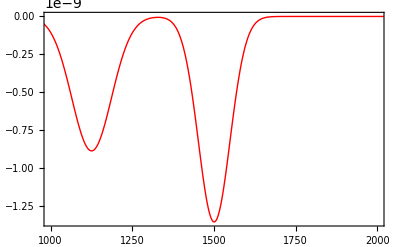

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

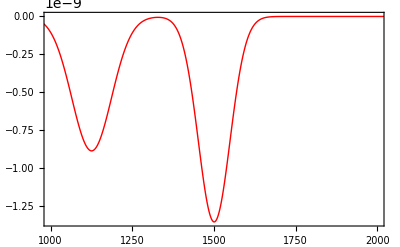

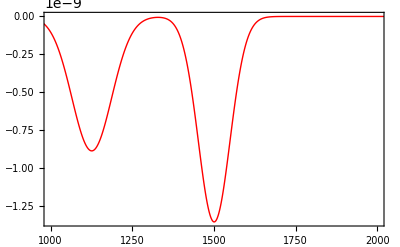

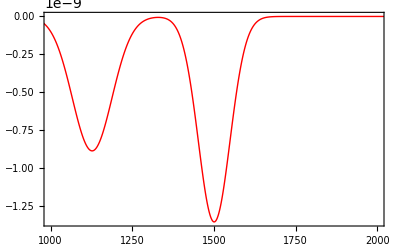

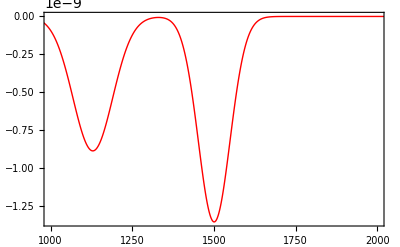

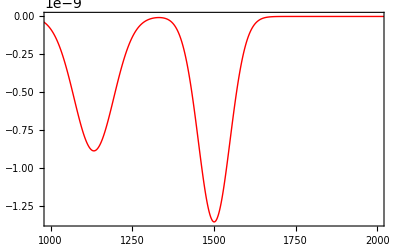

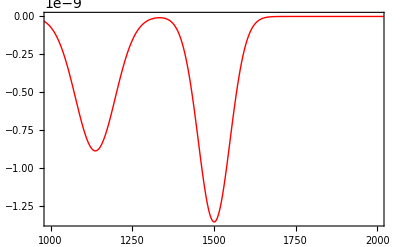

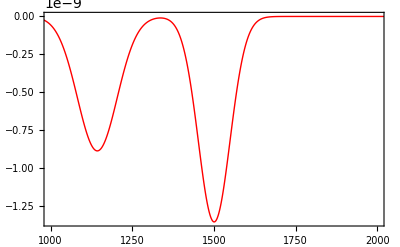

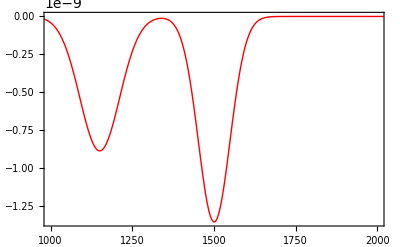

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

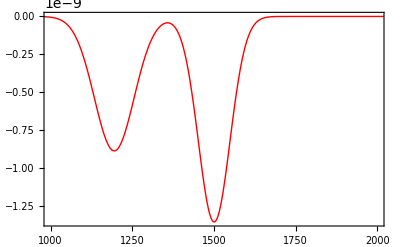

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

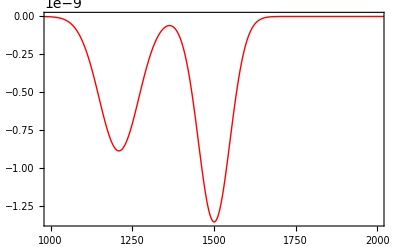

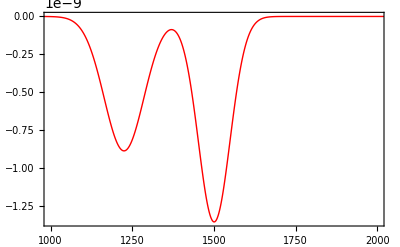

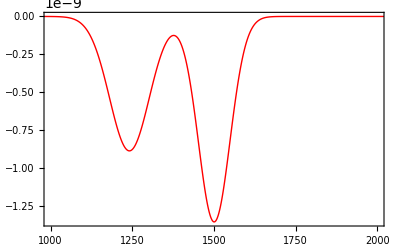

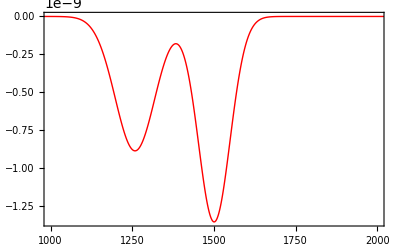

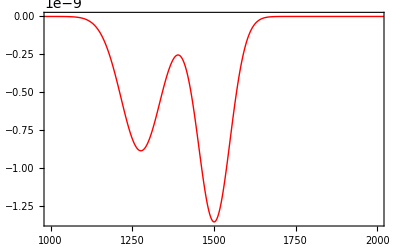

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

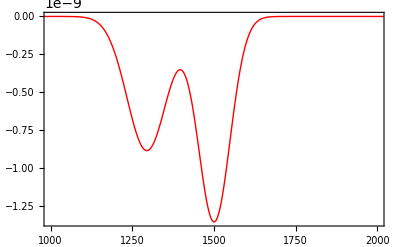

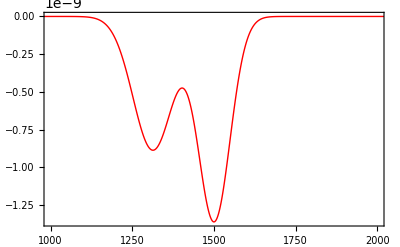

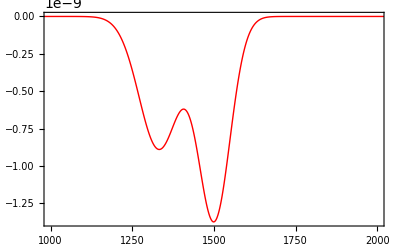

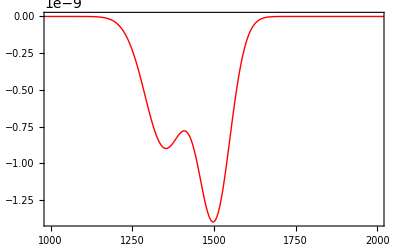

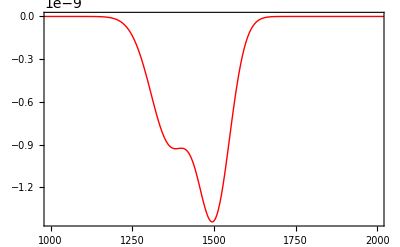

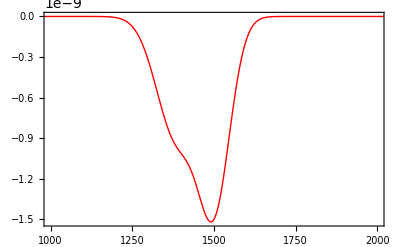

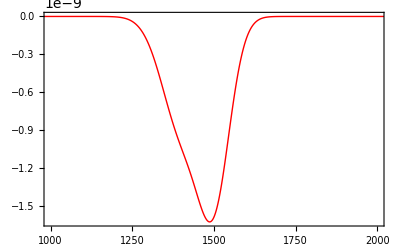

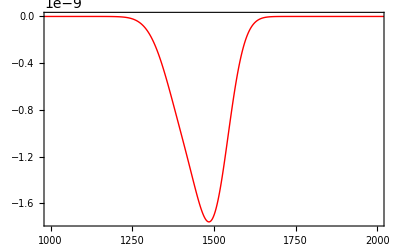

```mathematica
probeAxis="radial";
probeAtom="Na";

tMerge=3.8;(*ms*)
dt=.1; (*ms*)
dMerge=2.5; (*um*)

tLower=1.4(*ms*);
(*t, dx, power*)
paramsList=Table[{t,
If[t≤tMerge,dMerge(1-(10 (t/tMerge)^3-15(t/tMerge)^4+ 6 (t/tMerge)^5)),0],
If[t≤tMerge,power,power(1-(t-tMerge)/tLower)]

},{t,0,tMerge+tLower,dt}];

padleft=Ceiling[Log[10,1/dt]];
padright=Ceiling[Log[10,(tMerge+tLower)/dt]];

listmerge=Reap[
Do[
Nasol=FindMinimum[fnNa[x,params[[2]],0]/.p->params[[3]] mW ,{x,0}];
Cssol=FindMinimum[fnCs[x,params[[2]],0]/.p->params[[3]] mW,{{x,-params[[2]]}}];
(*lower bound on 976 = upper bound on 700: don't want 700 to cancel out 976 for Cs
lower bound on Na = upper bound on 976: avoid double well for Na
*)

Csaxial[z_]:=fnCs[x,params[[2]],z]/.p->params[[3]] mW /.Last[Cssol];
Naaxial[z_]:=fnNa[x,params[[2]],z]/.p->params[[3]] mW /.Last[Nasol];

Nasolax=FindMinimum[Naaxial[z]/.p->params[[3]] mW  ,{z,defocus}];
Cssolax=FindMinimum[Csaxial[z]/.p->params[[3]] mW ,{{z,0}}];

zmin=-10; (*in μm*)
zmax=10;
nn=3000;
(*what potential to export*)
If[probeAtom=="Cs",
If[probeAxis=="axial",

CsExp=Table[Csaxial[z a0/μm]mK kb/Hartree,{z,zmin μm/a0,zmax μm/a0,(zmax μm/a0-zmin μm/a0)/(nn-1)}],

CsExp=Table[fnCs[x a0/μm,params[[2]] ,0]mK kb/Hartree/.p->params[[3]] mW,
{x,zmin μm/a0,zmax μm/a0,(zmax μm/a0-zmin μm/a0)/(nn-1)}]],


If[probeAxis=="axial",

CsExp=Table[Naaxial[z a0/μm]mK kb/Hartree,{z,zmin μm/a0,zmax μm/a0,(zmax μm/a0-zmin μm/a0)/(nn-1)}],

CsExp=Table[fnNa[x a0/μm,params[[2]] ,0]mK kb/Hartree/.p->params[[3]] mW,
{x,zmin μm/a0,zmax μm/a0,(zmax μm/a0-zmin μm/a0)/(nn-1)}]]

];

Print[ListPlot[CsExp,Joined->True,PlotRange->{{nn/2-500,nn/2+500},All}]];

SetDirectory[NotebookDirectory[]];
Export["pot"<>StringPadLeft[ToString[Round[params[[1]] 10^padleft]],padleft+padright,"0"]<>".csv",CsExp];

Sow[{
(*radial potentials*)
Show[{
Plot[{
(*Na potential*)
fnNa[x,params[[2]],0]/.p->params[[3]] mW ,
(*Cs potential*)
fnCs[x,params[[2]],0]/.p->params[[3]] mW 

},{x,-4.5,4.5},PlotRange->{All,{-3,1.5}}
,PlotStyle->{{Orange,Thick},{Blue,Thick}},FrameLabel->{Style["Position (μm)",sty3],Style["Trap Depth (mK)",sty3]}, FrameStyle->Directive[Black,12]
(*,PlotLabel->Style["Na and Cs ODTs",sty3],PlotLegends->Placed[{Style["Na",sty2],Style["Cs",sty2]},{Right,Bottom}]*)],

ListPlot[{
{{x+xoffs/.Nasol[[2]],Nasol[[1]]+offs}},
{{x+xoffs/.Cssol[[2]],Cssol[[1]]+offs}}
}]
}
]

,
(*axial potentials*)
Show[{
Plot[{
(*Na potential*)
Naaxial[z] ,
(*Cs potential*)
Csaxial[z] 

},{z,zmin,zmax},PlotRange->{All,{-3,1.5}}
,PlotStyle->{{Orange,Thick},{Blue,Thick}},FrameLabel->{Style["Position (μm)",sty3],Style["Trap Depth (mK)",sty3]}, FrameStyle->Directive[Black,12]
(*,PlotLabel->Style["Na and Cs ODTs",sty3],PlotLegends->Placed[{Style["Na",sty2],Style["Cs",sty2]},{Right,Bottom}]*)],

ListPlot[{
{{z+xoffs/.Nasolax[[2]],Nasolax[[1]]+offs}},
{{z+xoffs/.Cssolax[[2]],Cssolax[[1]]+offs}}

}]
}
]
}]
,{params,paramsList}]
][[2,1]];

Export["params.csv",Join[{zmin,zmax,nn},paramsList[[;;,1]]]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*list=Join[listmerge,listlower];*)
list=GraphicsGrid[{{listmerge[[#,1]]},{listmerge[[#,2]]}}]&/@Range[Length[listmerge]];
(*add legend and other postprocessing*)
legendloc={270,-120};{3.1,-1.8};{1.8,1.8};

list2=Show[list[[#]],Epilog->{
Style[Text[ToString[dt(#-1)]<>" ms",{300,-30}],20],
Style[Text["-",legendloc],Blue,Bold,20],Style[Text["Cs",legendloc+{40,0}],20],
Style[Text["-",legendloc+{0,-30}],Orange,Bold,20],Style[Text["Na",legendloc+{40,0}+{0,-30}],20]}]&/@Range[Length[list]];

Export["animation.gif",list2]
```

animation.gif

# plot

## estimate the axial and radial freqs (to check w matlab answer):

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

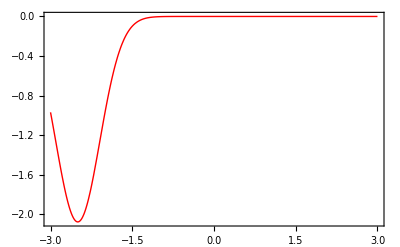

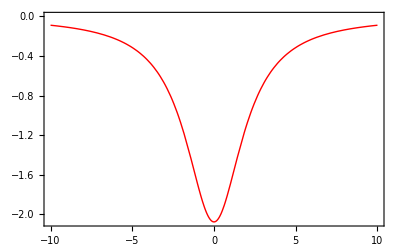

33.8974

38.4339

0.+0.0555256 ⅈ

141.715

```mathematica
params={0,2.5,0};
Nasol=FindMinimum[fnNa[x,params[[2]],0]/.p->params[[3]] mW ,{x,0}];
Cssol=FindMinimum[fnCs[x,params[[2]],0]/.p->params[[3]] mW,{{x,-params[[2]]}}];
(*lower bound on 976 = upper bound on 700: don't want 700 to cancel out 976 for Cs
lower bound on Na = upper bound on 976: avoid double well for Na
*)

Csaxial[z_]:=fnCs[x,params[[2]],z]/.p->params[[3]] mW /.Last[Cssol];
Naaxial[z_]:=fnNa[x,params[[2]],z]/.p->params[[3]] mW /.Last[Nasol];

Nasolax=FindMinimum[Naaxial[z]/.p->params[[3]] mW  ,{z,defocus}];
Cssolax=FindMinimum[Csaxial[z]/.p->params[[3]] mW ,{{z,0}}];

Plot[fnCs[x,params[[2]],0]/.p->params[[3]] mW,{x,-3,3}]
Plot[Csaxial[z],{z,-10,10}]
√((2 kb)/(mNa μm^2)Coefficient[Series[Naaxial[z],{z,0,2}],z^2]mK)/2/π/kHz
√((2 kb)/(mCs μm^2)Coefficient[Series[Csaxial[z],{z,0,2}],z^2]mK)/2/π/kHz


√((2 kb)/(mNa μm^2)Coefficient[Series[fnNa[x,params[[2]],0]/.p->params[[3]] mW,{x,0,2}],x^2]mK)/2/π/kHz
√((2 kb)/(mCs μm^2)Coefficient[Series[fnCs[x,params[[2]],0]/.p->params[[3]] mW ,{x,-params[[2]],2}],x^2]mK)/2/π/kHz
```

```mathematica
√Coefficient[Series[fnNa[x,params[[2]],0]/.p->params[[3]] mW,{x,0,2}],x^2]/√Coefficient[Series[Naaxial[z],{z,0,2}],z^2]
√Coefficient[Series[fnCs[x,params[[2]],0]/.p->params[[3]] mW ,{x,-params[[2]],2}],x^2]/√Coefficient[Series[Csaxial[z],{z,0,2}],z^2]
```

0.+0.00163805 ⅈ

3.68723

```mathematica
(*compare polarizability of Na at 700 and 976*)
-u3D[x μm,0,λtrap,NaS]/.p->power mW /.{w0->.8μm,λtrap->700}/.x->0

-u3D[x μm,0,λtrap,NaS]/.p->power mW /.{w0->.8μm,λtrap->976}/.x->0

-u3D[x μm,0,λtrap,CsS]/.p->power mW /.{w0->.8μm,λtrap->700}/.x->0

-u3D[x μm,0,λtrap,CsS]/.p->power mW /.{w0->.8μm,λtrap->976}/.x->0
```

-0.278761

-0.128239

0.356225

-0.953072

# ANIMATED FIGURE!! WOOHOOO

```mathematica
sty={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->20,Black};
sty2={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->14,FontColor->Black,Bold};
sty3={FontFamily->"Helvetica",FontWeight->"Normal",FontSize->20,FontColor->Black,"Title"};
xoffs=0.02; (*horizontal offset for atom*)
offs=.15; (*vertical offset for atom*)
tMerge=3.8;(*ms*)
dtMerge=.1; (*ms*)
dMerge=2.5; (*um*)
dx=.03;(*resolution of minimum-finding*)
yList=Table[dMerge(1-(10 (t/tMerge)^3-15(t/tMerge)^4+ 6 (t/tMerge)^5)),{t,0,tMerge,dtMerge}];
tLower=1.4(*ms*);
dtLower=.1(*ms*);

powerList=power Table[(1-t/tLower),{t,0,tLower,dtLower}];

(*to track minimum of potential*)
listmerge=Table[
Show[{
Plot[{
(*Na potential*)
fnNa[x,y,0]/.p->power mW ,
(*Cs potential*)
fnCs[x,y,0]/.p->power mW 

},{x,-4.5,4.5},PlotRange->{All,{-3,1.5}}
,PlotStyle->{{Orange,Thick},{Blue,Thick}},FrameLabel->{Style["Position (μm)",sty3],Style["Trap Depth (mK)",sty3]}, FrameStyle->Directive[Black,12]
(*,PlotLabel->Style["Na and Cs ODTs",sty3],PlotLegends->Placed[{Style["Na",sty2],Style["Cs",sty2]},{Right,Bottom}]*)]
,

ListPlot[{
(*Na atom*)
{SortBy[Table[{x+xoffs,offs+fnNa[x,y,0]/.p->power mW },{x,-5,0,dx}],Last][[1]]
},
(*Cs atom*)
{SortBy[Table[{x+xoffs,offs+fnCs[x,y,0]/.p->power mW },{x,-5,0,dx}],Last][[1]]
}
},PlotMarkers->Automatic]
}]
,{y,yList}
];

listlower=Table[
Show[{
Plot[{
(*Na potential*)
fnNa[x,0,0]/.p->powerV mW ,
(*Cs potential*)
fnCs[x,0,0]/.p->powerV mW 

},{x,-4.5,4.5},PlotRange->{All,{-3,1.5}}
,PlotStyle->{{Orange,Thick},{Blue,Thick}},FrameLabel->{Style["Position (μm)",sty3],Style["Trap Depth (mK)",sty3]}, FrameStyle->Directive[Black,12]
(*,PlotLabel->Style["Na and Cs ODTs",sty3],PlotLegends->Placed[{Style["Na",sty2],Style["Cs",sty2]},{Right,Bottom}]*)
]
,
ListPlot[{
(*Na atom*)
{SortBy[Table[{x+xoffs,offs+fnNa[x,0,0]/.p->powerV mW },{x,-5,0,dx}],Last][[1]]
},
(*Cs atom*)
{SortBy[Table[{x+xoffs,offs+fnCs[x,0,0]/.p->powerV mW},{x,-5,0,dx}],Last][[1]]
}
},PlotMarkers->Automatic]
}]

,{powerV,powerList}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
list=Join[listmerge,listlower];
(*add legend and other postprocessing*)
legendloc={3.1,-1.8};{1.8,1.8};

list2=Show[list[[#]],Epilog->{
Style[Text[ToString[If[#<Length[listmerge],dtMerge,dtLower](#-1)]<>" ms",{3,.75}],20],
Style[Text["-",legendloc],Blue,Bold,20],Style[Text["Cs",legendloc+{.8,0}],20],
Style[Text["-",legendloc+{0,-.6}],Orange,Bold,20],Style[Text["Na",legendloc+{.8,0}+{0,-.6}],20]}]&/@Range[Length[list]];
Export["animation.gif",list2]
```

animation.gif

## make the paper figure---- add real pics of tweezers?

```mathematica
(*SetOptions[Plot,PlotStyle->{Orange,Blue},
Prolog->Flatten@{Directive[lineStyle],lines},
LabelStyle->{Larger,Black,Bold}
];*)
```

```mathematica
mergeplotlabels[[2]]
```

Part::partd: Part specification mergeplotlabels⟦2⟧ is longer than depth of object.

mergeplotlabels⟦2⟧

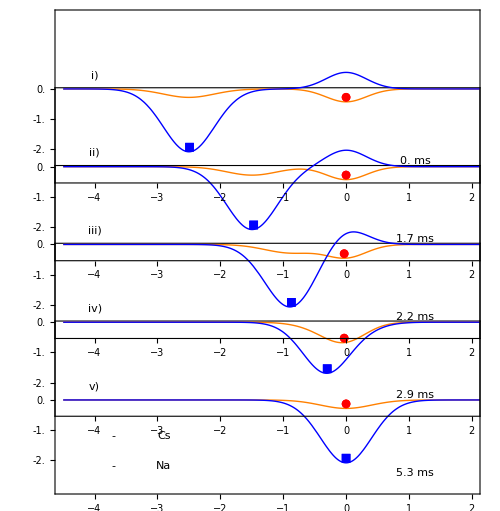

merge_potentials.pdf

```mathematica
Clear[figopts];
frametickssty={Black,20};
figplots={1,18,23,30,Length[list]};
figopts=
{PlotRange->{{-4.5,2},{-3,2.5}},
FrameLabel->{Null,Null,Null,Null},Frame->{True,True,False,True},
FrameTicks->{Automatic,Range[-2.,0,1],Automatic,Automatic},
FrameTicksStyle->{frametickssty,Directive[FontOpacity->0,FontSize->0]},
PlotLabel->Null,Axes->False,
PlotRangePadding->None,FrameStyle->AbsoluteThickness[.01],Axes->False,AspectRatio->.4,
ImagePadding->{{70,10},{60,10}}(*{L,R},{B,T}*)
};
imagesize=500;


legendloc={-3.7,-1.2};
mergeplotlabels={"i)","ii)","iii)","iv)","v)"};

list3=Show[list[[#]],Prolog->
{(*label*)
Style[Text[If[MemberQ[figplots,#],mergeplotlabels[[Position[figplots,#][[1]]]][[1]],""],{-4.,.46}],20],

(*timing*)
Style[Text[ToString[If[#<Length[listmerge],dtMerge,dtLower](#-1)]<>" ms",{1.1,-2.4}],20],

(*legend*)
Style[Text[If[#==Length[list],"-",""],legendloc],Blue,Bold,20],

Style[Text[If[#==Length[list],"Cs",""],legendloc+{.8,0}],20],

Style[Text[If[#==Length[list],"-",""],legendloc+{0,-1}],Orange,Bold,20],

Style[Text[If[#==Length[list],"Na",""],legendloc+{.8,-1}],20]
}]&/@Range[Length[list]];

GraphicsColumn[
Join[
{Show[list3[[figplots[[1]]]],Frame->True,figopts
]},

Show[list3[[#]],figopts]&/@figplots[[2;;-2]],

{Show[list3[[-1]],FrameLabel->{Style["Position[μm]",frametickssty]}, FrameTicksStyle->{frametickssty,frametickssty},figopts]}

][[-1;;1;;-1]]
,ImageSize->imagesize,Spacings->-200,

Epilog->Rotate[Style[Text["Trap Depth [mK]",{85,imagesize/3.5}],frametickssty],π/2]

]


Export["merge_potentials.pdf",%]
```